```mathematica
libraryPath = "PATH TO .dylib FILE";
billmin=LibraryFunctionLoad[libraryPath,"minimize",{Real, Real, Integer, Real},NumericArray]
zout=LibraryFunctionLoad[libraryPath,"zoutside",{Real, Real},NumericArray]
zin=LibraryFunctionLoad[libraryPath,"zinside",{Real, Real},NumericArray]
```

LibraryFunction[…]

LibraryFunction[…]

LibraryFunction[…]

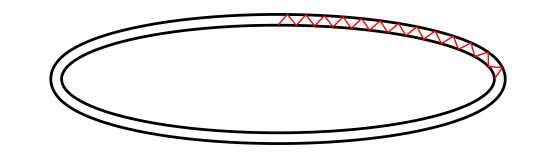

```mathematica
si = 0;
n = 25;
δ = .1;
ParametricPlot[
{
Normal[zin[s, δ]], 
Normal[zout[s, δ]]
},
{s, 0,2Pi} ,
Epilog->
{Red,Line[
Join[ 
Normal[zout[si,δ]],
Normal[billmin[si,Pi/2, n, δ]],
 If[ OddQ[n],Normal[zout[Pi/2, δ]], Normal[zin[Pi/2, δ]]]
]
]
},
PlotStyle->Black,
AxesStyle->Thick,
TicksStyle->Directive[16],
Axes->False,
Ticks->False
]
```

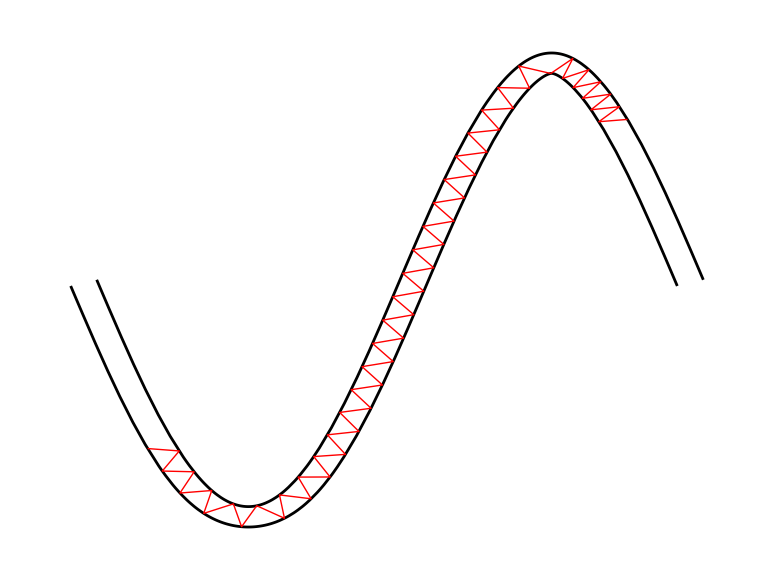

```mathematica
Show[%8,AspectRatio->.75]
```

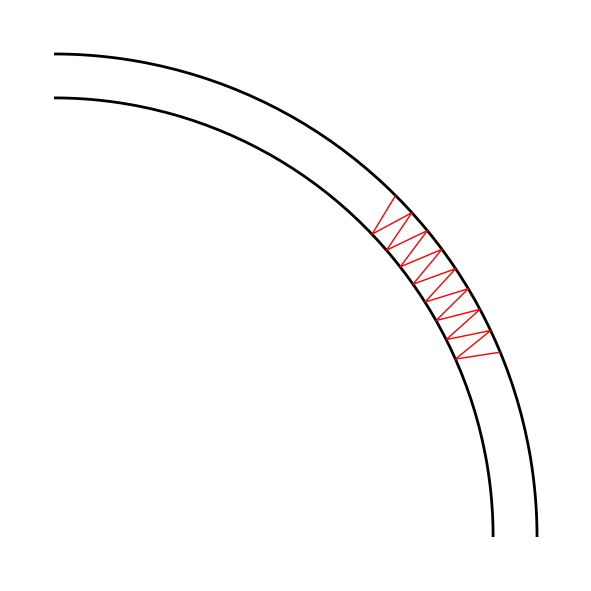

```mathematica
With[
{
si = Pi/4,
sf = Pi/8,
n = 15,
δ = .1
},
ParametricPlot[
{
Normal[zin[s, δ]], 
Normal[zout[s, δ]]
},
{s, 0,Pi/2} ,
Epilog->
{Red,Line[
Join[Normal[zin[si,δ]],
Normal[billmin[si,sf, n, δ]],
 If[ EvenQ[n],Normal[zout[sf, δ]], Normal[zin[sf, δ]]]]
]},
PlotStyle->Black,
AxesStyle->Thick,
TicksStyle->Directive[16],
Axes->False,
Ticks->False,
AspectRatio->1
]
]
```

```mathematica
{{0,-1},{1,0}}.D[{(1.25 + Cos[s])Cos[s], (1.25 + Cos[s])Sin[s]},s]
```

{-Cos[s] (1.25+Cos[s])+Sin[s]^2,-Cos[s] Sin[s]-(1.25+Cos[s]) Sin[s]}